```mathematica
ex = {1,0, 0};
ey = {0,1, 0};
ez = {0, 0, 1};
r10 = {-dx, 0, 0};
r20 = {dx, 0, 0};

θ1 = y1[t];
θ2 = y2[t];
x = y3[t];

ω1 = D[θ1, t];
ω2 = D[θ2, t];
v = D[x,t];

α1 = D[ω1, t];
α2 = D[ω2, t];
a = D[v,t];

r1 = r10 + l {Sin[θ1], -Cos[θ1], 0};
r2 = r20 + l {Sin[θ2], -Cos[θ2], 0};

v0 = {v, 0, 0};
v1 = v0 + (ω1 ez)×(r1 - r10)
v2 = v0 + (ω2 ez)×(r2 - r20)

PE = m g (Dot[r1,ey] + Dot[r2,ey])
KE = 1/2 M Dot[v0,v0] + 1/2 m Dot[v1,v1] + 1/2 m Dot[v2,v2]
L = Simplify[KE-PE]
(* Dissipative Forces *)
Q = - μ m g(v / Abs[v])  -b l^2 ω1 - b l^2 ω2
(*Lalt = Simplify[1/2(M+2 m)v^2 + m v l (Cos[θ1]ω1 + Cos[θ2]ω2) + 1/2 m l^2(ω1^2+ω2^2) + m g l(Cos[θ1] + Cos[θ2])];
Simplify[L - Lalt]*)

(* Clock Force *)
αc1 = Piecewise[{
{αc, -θb < θ1 && θ1 < -θa}
(*{-αc, θa < θ1 && θ1 < θb}*)
}, 0]
αc2 = Piecewise[{
{αc, -θb < θ2 && θ2 < -θa}
(*{-αc, θa < θ2 && θ2 < θb}*)
}, 0]
```

{l Cos[y1[t]] y1'[t]+y3'[t],l Sin[y1[t]] y1'[t],0}

{l Cos[y2[t]] y2'[t]+y3'[t],l Sin[y2[t]] y2'[t],0}

g m (-l Cos[y1[t]]-l Cos[y2[t]])

1/2 M y3'[t]^2+1/2 m (l^2 Sin[y1[t]]^2 y1'[t]^2+(l Cos[y1[t]] y1'[t]+y3'[t])^2)+1/2 m (l^2 Sin[y2[t]]^2 y2'[t]^2+(l Cos[y2[t]] y2'[t]+y3'[t])^2)

1/2 (2 g l m Cos[y1[t]]+2 g l m Cos[y2[t]]+l^2 m y1'[t]^2+l^2 m y2'[t]^2+2 l m Cos[y1[t]] y1'[t] y3'[t]+2 l m Cos[y2[t]] y2'[t] y3'[t]+2 m y3'[t]^2+M y3'[t]^2)

-b l^2 y1'[t]-b l^2 y2'[t]-(g m μ y3'[t])/Abs[y3'[t]]

Piecewise[{{αc, -θb<y1[t]&&y1[t]<-θa}, {0, True}}]

Piecewise[{{αc, -θb<y2[t]&&y2[t]<-θa}, {0, True}}]

```mathematica
Simplify[D[D[L,ω1],t]/.{y1->"θ1", y2->"θ2", y3->"x"}]
Simplify[D[L,θ1]/.{y1->"θ1", y2->"θ2", y3->"x"}]
```

l m (-Sin[θ1[t]] x'[t] θ1'[t]+Cos[θ1[t]] x''[t]+l θ1''[t])

-l m Sin[θ1[t]] (g+x'[t] θ1'[t])

```mathematica
repr = {y1->"θ1", y2->"θ2", y3->"x"};
eq1 = Simplify[D[D[L,ω1],t] - D[L,θ1] == -b l^2 ω1 + αc1];
eq2 = Simplify[D[D[L,ω2],t]-  D[L,θ2] == -b l^2 ω2 + αc2]; 
eq3 = Simplify[D[D[L,v],t]- D[L, x] == - bx v ];(*-μ( 2 m+M) g Sign[v] - b v] ;*)
eq1/.repr
eq2/.repr
eq3/.repr
```

(Piecewise[{{αc, θb+θ1[t]>0&&θa+θ1[t]<0}, {0, True}}])==l (b l θ1'[t]+m (g Sin[θ1[t]]+Cos[θ1[t]] x''[t]+l θ1''[t]))

(Piecewise[{{αc, θb+θ2[t]>0&&θa+θ2[t]<0}, {0, True}}])==l (b l θ2'[t]+m (g Sin[θ2[t]]+Cos[θ2[t]] x''[t]+l θ2''[t]))

bx x'[t]+2 m x''[t]+M x''[t]+l m Cos[θ1[t]] θ1''[t]+l m Cos[θ2[t]] θ2''[t]==l m (Sin[θ1[t]] θ1'[t]^2+Sin[θ2[t]] θ2'[t]^2)

```mathematica
sol = Simplify[Solve[{eq1,eq2,eq3}, {y1''[t], y2''[t], y3''[t]}]]
```

{{y1''[t]→1/(l^2 m (-2 m-M+m Cos[y1[t]]^2+m Cos[y2[t]]^2))((-2 m-M+m Cos[y2[t]]^2) (Piecewise[{{αc, θb+y1[t]>0&&θa+y1[t]<0}, {0, True}}])-m Cos[y1[t]] Cos[y2[t]] (Piecewise[{{αc, θb+y2[t]>0&&θa+y2[t]<0}, {0, True}}])+l (b l (2 m+M-m Cos[y2[t]]^2) y1'[t]+l m^2 Cos[y1[t]] Sin[y1[t]] y1'[t]^2+m (1/2 g ((3 m+2 M) Sin[y1[t]]-m Sin[y1[t]-2 y2[t]])+b l Cos[y1[t]] Cos[y2[t]] y2'[t]+l m Cos[y1[t]] Sin[y2[t]] y2'[t]^2-bx Cos[y1[t]] y3'[t]))),y2''[t]→1/(l^2 m (-2 (m+M)+m Cos[2 y1[t]]+m Cos[2 y2[t]]))(-2 m Cos[y1[t]] Cos[y2[t]] (Piecewise[{{αc, θb+y1[t]>0&&θa+y1[t]<0}, {0, True}}])+(-3 m-2 M+m Cos[2 y1[t]]) (Piecewise[{{αc, θb+y2[t]>0&&θa+y2[t]<0}, {0, True}}])+l (2 b l m Cos[y1[t]] Cos[y2[t]] y1'[t]+2 l m^2 Cos[y2[t]] Sin[y1[t]] y1'[t]^2-b l (-3 m-2 M+m Cos[2 y1[t]]) y2'[t]+l m^2 Sin[2 y2[t]] y2'[t]^2+m (g (m Sin[2 y1[t]-y2[t]]+(3 m+2 M) Sin[y2[t]])-2 bx Cos[y2[t]] y3'[t]))),y3''[t]→-1/(l (-2 (m+M)+m Cos[2 y1[t]]+m Cos[2 y2[t]]))2 (-Cos[y1[t]] (Piecewise[{{αc, θb+y1[t]>0&&θa+y1[t]<0}, {0, True}}])-Cos[y2[t]] (Piecewise[{{αc, θb+y2[t]>0&&θa+y2[t]<0}, {0, True}}])+l (g m Cos[y1[t]] Sin[y1[t]]+g m Cos[y2[t]] Sin[y2[t]]+b l Cos[y1[t]] y1'[t]+l m Sin[y1[t]] y1'[t]^2+b l Cos[y2[t]] y2'[t]+l m Sin[y2[t]] y2'[t]^2-bx y3'[t]))}}

```mathematica
(*(deqn = {a - γv}/.sol[[1]]*)
deqnl = List @@@ (Equal @@@ sol[[1]]);
deqnlhs = deqnl[[All, 1]];
deqnrhs = deqnl[[All, 2]];
deqnrhs = deqnrhs + {αc1,αc2, 0};
(*deqn = Equal @@@Transpose[{deqnlhs, deqnrhs}]*)
deqn = Equal @@@ sol[[1]]
```

{y1''[t]==1/(l^2 m (-2 m-M+m Cos[y1[t]]^2+m Cos[y2[t]]^2))((-2 m-M+m Cos[y2[t]]^2) (Piecewise[{{αc, θb+y1[t]>0&&θa+y1[t]<0}, {0, True}}])-m Cos[y1[t]] Cos[y2[t]] (Piecewise[{{αc, θb+y2[t]>0&&θa+y2[t]<0}, {0, True}}])+l (b l (2 m+M-m Cos[y2[t]]^2) y1'[t]+l m^2 Cos[y1[t]] Sin[y1[t]] y1'[t]^2+m (1/2 g ((3 m+2 M) Sin[y1[t]]-m Sin[y1[t]-2 y2[t]])+b l Cos[y1[t]] Cos[y2[t]] y2'[t]+l m Cos[y1[t]] Sin[y2[t]] y2'[t]^2-bx Cos[y1[t]] y3'[t]))),y2''[t]==1/(l^2 m (-2 (m+M)+m Cos[2 y1[t]]+m Cos[2 y2[t]]))(-2 m Cos[y1[t]] Cos[y2[t]] (Piecewise[{{αc, θb+y1[t]>0&&θa+y1[t]<0}, {0, True}}])+(-3 m-2 M+m Cos[2 y1[t]]) (Piecewise[{{αc, θb+y2[t]>0&&θa+y2[t]<0}, {0, True}}])+l (2 b l m Cos[y1[t]] Cos[y2[t]] y1'[t]+2 l m^2 Cos[y2[t]] Sin[y1[t]] y1'[t]^2-b l (-3 m-2 M+m Cos[2 y1[t]]) y2'[t]+l m^2 Sin[2 y2[t]] y2'[t]^2+m (g (m Sin[2 y1[t]-y2[t]]+(3 m+2 M) Sin[y2[t]])-2 bx Cos[y2[t]] y3'[t]))),y3''[t]==-1/(l (-2 (m+M)+m Cos[2 y1[t]]+m Cos[2 y2[t]]))2 (-Cos[y1[t]] (Piecewise[{{αc, θb+y1[t]>0&&θa+y1[t]<0}, {0, True}}])-Cos[y2[t]] (Piecewise[{{αc, θb+y2[t]>0&&θa+y2[t]<0}, {0, True}}])+l (g m Cos[y1[t]] Sin[y1[t]]+g m Cos[y2[t]] Sin[y2[t]]+b l Cos[y1[t]] y1'[t]+l m Sin[y1[t]] y1'[t]^2+b l Cos[y2[t]] y2'[t]+l m Sin[y2[t]] y2'[t]^2-bx y3'[t]))}

```mathematica
params={
m-> 0.080,
M-> 10.0,
g-> 9.8,
l -> 0.4,
dx -> 0.3,
μ -> 0.2,
b -> 0.001,
bx -> 0.1,
θa-> 5 °,
θb -> 7 °,
αc ->0.1
};
(2 π √l/g) /. params (* period *)
dinit ={
y1[0]==6°, y2[0]==-6 °, y3[0]==0,
y1'[0]==0.0, y2'[0]==0, y3'[0]==0
}
deqn/.params
tfin = 100;
dsol = NDSolve[Join[deqn /. params,dinit], {y1[t],y2[t],y3[t] , y1'[t], y2'[t], y3'[t]},{t,0,tfin},
Method->{Automatic,"DiscontinuityProcessing"->False}
]
```

1.2694

{y1[0]==6 °,y2[0]==-6 °,y3[0]==0,y1'[0]==0.,y2'[0]==0,y3'[0]==0}

{y1''[t]==1/(-10.16+0.08 Cos[y1[t]]^2+0.08 Cos[y2[t]]^2)78.125 ((-10.16+0.08 Cos[y2[t]]^2) (Piecewise[{{0.1, 7 °+y1[t]>0&&5 °+y1[t]<0}, {0, True}}])-0.08 Cos[y1[t]] Cos[y2[t]] (Piecewise[{{0.1, 7 °+y2[t]>0&&5 °+y2[t]<0}, {0, True}}])+0.4 (0.0004 (10.16-0.08 Cos[y2[t]]^2) y1'[t]+0.00256 Cos[y1[t]] Sin[y1[t]] y1'[t]^2+0.08 (4.9 (20.24 Sin[y1[t]]-0.08 Sin[y1[t]-2 y2[t]])+0.0004 Cos[y1[t]] Cos[y2[t]] y2'[t]+0.032 Cos[y1[t]] Sin[y2[t]] y2'[t]^2-0.1 Cos[y1[t]] y3'[t]))),y2''[t]==1/(-20.16+0.08 Cos[2 y1[t]]+0.08 Cos[2 y2[t]])78.125 (-0.16 Cos[y1[t]] Cos[y2[t]] (Piecewise[{{0.1, 7 °+y1[t]>0&&5 °+y1[t]<0}, {0, True}}])+(-20.24+0.08 Cos[2 y1[t]]) (Piecewise[{{0.1, 7 °+y2[t]>0&&5 °+y2[t]<0}, {0, True}}])+0.4 (0.000064 Cos[y1[t]] Cos[y2[t]] y1'[t]+0.00512 Cos[y2[t]] Sin[y1[t]] y1'[t]^2-0.0004 (-20.24+0.08 Cos[2 y1[t]]) y2'[t]+0.00256 Sin[2 y2[t]] y2'[t]^2+0.08 (9.8 (0.08 Sin[2 y1[t]-y2[t]]+20.24 Sin[y2[t]])-0.2 Cos[y2[t]] y3'[t]))),y3''[t]==-1/(-20.16+0.08 Cos[2 y1[t]]+0.08 Cos[2 y2[t]])5. (-Cos[y1[t]] (Piecewise[{{0.1, 7 °+y1[t]>0&&5 °+y1[t]<0}, {0, True}}])-Cos[y2[t]] (Piecewise[{{0.1, 7 °+y2[t]>0&&5 °+y2[t]<0}, {0, True}}])+0.4 (0.784 Cos[y1[t]] Sin[y1[t]]+0.784 Cos[y2[t]] Sin[y2[t]]+0.0004 Cos[y1[t]] y1'[t]+0.032 Sin[y1[t]] y1'[t]^2+0.0004 Cos[y2[t]] y2'[t]+0.032 Sin[y2[t]] y2'[t]^2-0.1 y3'[t]))}

{{y1[t]→InterpolatingFunction[{{0., 100.}}, <>][t],y2[t]→InterpolatingFunction[{{0., 100.}}, <>][t],y3[t]→InterpolatingFunction[{{0., 100.}}, <>][t],y1'[t]→InterpolatingFunction[{{0., 100.}}, <>][t],y2'[t]→InterpolatingFunction[{{0., 100.}}, <>][t],y3'[t]→InterpolatingFunction[{{0., 100.}}, <>][t]}}

```mathematica
nδs = Table[(θ1-θ2)/° /. params /. dsol[[1]], {t, 0, tfin,tfin/1000}];
nσs = Table[(θ1+θ2)/° /. params /. dsol[[1]], {t, 0, tfin, tfin/1000}];
nxs = Table[x/.params/.dsol[[1]], {t, 0, tfin,tfin/1000}];
nvs = Table[v/.params/.dsol[[1]], {t, 0, tfin, tfin/1000}];
nas = Table[αc1 /.params/.dsol[[1]], {t, 0, tfin, tfin/1000}];
```

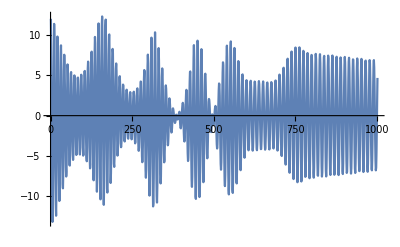

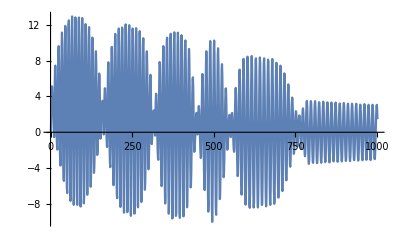

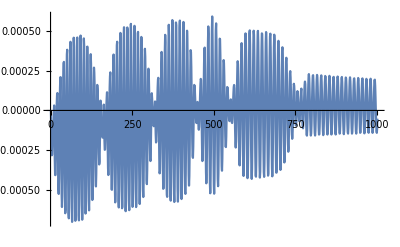

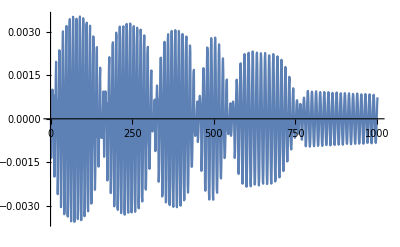

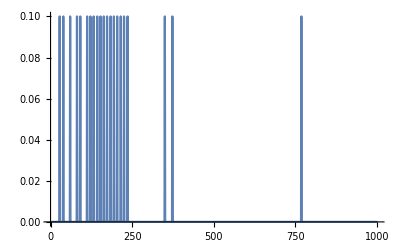

```mathematica
ListLinePlot[nδs]
ListLinePlot[nσs]
ListLinePlot[nxs]
ListLinePlot[nvs]
ListLinePlot[nas]
```

```mathematica
nr2s = Table[r2[[;;2]]/.params/.dsol[[1]], {t,0,100, 0.01}];
(*Dimensions[nr2s][[1]]
Length[nr2s]
ListLinePlot[nr2s[[;;6, All]]]*)
range ={MinMax[nr2s[[All,1]]], MinMax[nr2s[[All, 2]]]}
ar = (range[[2,2]] - range[[2,1]])/(range[[1,2]] - range[[1,1]])
(*Show[
ListLinePlot[nr2s[[;;100, All]] , PlotRange->range, AspectRatio->1],
Graphics[Disk[nr2s[[100,All]], 0.005 {1, ar}]],
AspectRatio->1,
PlotRange->range
]*)

(*Animate[Show[
ListLinePlot[nr2s[[;;n, All]] , PlotRange->range, AspectRatio->1],
Graphics[Disk[nr2s[[n,All]], 0.005 {1, ar}]],
AspectRatio->1,
PlotRange->range
],{n,1,Length[nr2s], 1}
]*)

(*Plot[y3[t]/.params/.dsol, {t,0,1000}]
Plot[Evaluate[{r2-r20, r1-r10}/.params/.dsol], {t,0,1000}]*)
```

{{0.258189,0.358849},{-0.4,-0.395647}}

0.043241

```mathematica
(* auxiliary stuff *)
DSolve[D[{θ[t],ω[t]},t] == {ω[t], -b ω[t] -m g Sin[θ[t]]}, θ[t]]
```

DSolve::argm: DSolve called with 2 arguments; 3 or more arguments are expected.

DSolve[{θ'[t],ω'[t]}=={ω[t],-g m Sin[θ[t]]-b ω[t]},θ[t]]

{(ⅇ^(-1/2 (b+√(b^2-4 g m)) t) (2 (-1+ⅇ^(√(b^2-4 g m) t)) vy0+(b (-1+ⅇ^(√(b^2-4 g m) t))+(1+ⅇ^(√(b^2-4 g m) t)) √(b^2-4 g m)) y0))/(2 √(b^2-4 g m))}

{(ⅇ^(-1/2 (b+√(b^2-4 g m)) t) (-b (-1+ⅇ^(√(b^2-4 g m) t)) vy0+(1+ⅇ^(√(b^2-4 g m) t)) √(b^2-4 g m) vy0-2 (-1+ⅇ^(√(b^2-4 g m) t)) g m y0))/(2 √(b^2-4 g m))}

{1/8 l m ((ⅇ^(-(b+√(b^2-4 g m)) t) l (b (-1+ⅇ^(√(b^2-4 g m) t)) vy0-(1+ⅇ^(√(b^2-4 g m) t)) √(b^2-4 g m) vy0+2 (-1+ⅇ^(√(b^2-4 g m) t)) g m y0)^2)/(b^2-4 g m)-8 g (1-(ⅇ^(-(b+√(b^2-4 g m)) t) (2 (-1+ⅇ^(√(b^2-4 g m) t)) vy0+(b (-1+ⅇ^(√(b^2-4 g m) t))+(1+ⅇ^(√(b^2-4 g m) t)) √(b^2-4 g m)) y0)^2)/(8 (b^2-4 g m))))}

{1/8 l m ((ⅇ^(-t (b+√(ω^2))) l (b (-1+ⅇ^(t √(ω^2))) vy0+2 (-1+ⅇ^(t √(ω^2))) g m y0-(1+ⅇ^(t √(ω^2))) vy0 √(ω^2))^2)/ω^2-8 g (1-(ⅇ^(-t (b+√(ω^2))) (2 (-1+ⅇ^(t √(ω^2))) vy0+y0 (b (-1+ⅇ^(t √(ω^2)))+(1+ⅇ^(t √(ω^2))) √(ω^2)))^2)/(8 ω^2)))}

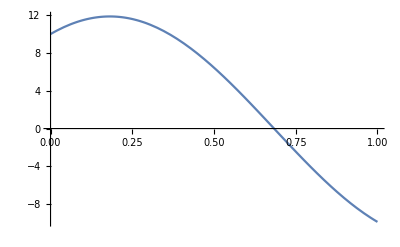

-Graphics-

-Graphics-

```mathematica
ysol = Simplify[yy[t] /. DSolve[{yy''[t] + b yy'[t] + m g yy[t]==0,yy[0]== y0, yy'[0] ==  vy0}, yy[t], t]]
dysol = Simplify[D[ysol, t]]
Simplify[1/2 m (l dysol)^2 - m g l (1-ysol^2/2)]
Simplify[% /. {(b^2-4 g m) -> ω^2}]

Plot[ysol/° /. {m->1, g->9.8, y0-> 10°, vy0-> 20°, b-> 0.01}, {t, 0, 1}]
(*Solve[{ysol[[1]]==0, t>0}, t]*)
Simplify[%]
%/.{m->1, g->9.8, y0-> 10°, vy0-> 20°, b-> 0.01}
```

```mathematica
/
```

```mathematica
Simplify[%]
```

{{yy[t]→(ⅇ^(-1/2 (b+√(b^2-4 g m)) t) (2 (-1+ⅇ^(√(b^2-4 g m) t)) vy0+(b (-1+ⅇ^(√(b^2-4 g m) t))+(1+ⅇ^(√(b^2-4 g m) t)) √(b^2-4 g m)) y0))/(2 √(b^2-4 g m))}}

```mathematica
% /. {yy -> θ, vy0 -> ω0, y0 -> θ0}
```

{{θ[t]→(ⅇ^(-1/2 (b+√(b^2-4 g m)) t) ((b (-1+ⅇ^(√(b^2-4 g m) t))+(1+ⅇ^(√(b^2-4 g m) t)) √(b^2-4 g m)) θ0+2 (-1+ⅇ^(√(b^2-4 g m) t)) ω0))/(2 √(b^2-4 g m))}}

```mathematica
TraditionalForm[%]
```

{{θ(t)→(ⅇ^(-1/2 t (√(b^2-4 g m)+b)) (θ0 (b (ⅇ^(t √(b^2-4 g m))-1)+√(b^2-4 g m) (ⅇ^(t √(b^2-4 g m))+1))+2 ω0 (ⅇ^(t √(b^2-4 g m))-1)))/(2 √(b^2-4 g m))}}

```mathematica
Reduce[Cos[-ϕ] == ⅇ^(-(b t)/(2 m))Cos[Subscript[ω, d] t-ϕ], t]
```

Reduce::nsmet: This system cannot be solved with the methods available to Reduce.

Reduce[Cos[ϕ]==ⅇ^(-(b t)/(2 m)) Cos[ϕ-t ω_d],t]